# Pendulum on an Incline

An inclined plane with height h and angle θ is fixed in place. A simple pendulum of length l and mass m is connected to a massless post also of length l and mounted on a thin platform of mass M that can slide down the plane without friction.

-Graphics-

```mathematica
Quit[]
```

```mathematica
X=s Cos[θ];
Xdot = sdot Cos[θ];
Y=-s Sin[θ];
Ydot=-sdot Sin[θ];
x=X+l*Sin[θ]+l*Sin[ϕ];
xdot=Xdot+l*Cos[ϕ]*ϕdot;
y=Y+l*Cos[θ]-l*Cos[ϕ];
ydot=Ydot+l*Sin[ϕ]*ϕdot;
```

```mathematica
T=1/2 M Xdot^2+1/2 M Ydot^2+1/2 m xdot^2+1/2 m ydot^2
U=M g Y+m g y
L=(T-U)//Simplify
```

1/2 M sdot^2 Cos[θ]^2+1/2 m (sdot Cos[θ]+l ϕdot Cos[ϕ])^2+1/2 M sdot^2 Sin[θ]^2+1/2 m (-sdot Sin[θ]+l ϕdot Sin[ϕ])^2

-g M s Sin[θ]+g m (l Cos[θ]-l Cos[ϕ]-s Sin[θ])

1/2 (m sdot^2+M sdot^2+l^2 m ϕdot^2-2 g l m Cos[θ]+2 g l m Cos[ϕ]+2 l m sdot ϕdot Cos[θ+ϕ]+2 g m s Sin[θ]+2 g M s Sin[θ])

```mathematica
ps=D[L,sdot]/.{s->s[t],sdot->s'[t],ϕ->ϕ[t],ϕdot->ϕ'[t]}
pϕ=D[L,ϕdot]/.{s->s[t],sdot->s'[t],ϕ->ϕ[t],ϕdot->ϕ'[t]}
ds=D[L,s]/.{s->s[t],sdot->s'[t],ϕ->ϕ[t],ϕdot->ϕ'[t]}
dϕ=D[L,ϕ]/.{s->s[t],sdot->s'[t],ϕ->ϕ[t],ϕdot->ϕ'[t]}
```

1/2 (2 m s'[t]+2 M s'[t]+2 l m Cos[θ+ϕ[t]] ϕ'[t])

1/2 (2 l m Cos[θ+ϕ[t]] s'[t]+2 l^2 m ϕ'[t])

1/2 (2 g m Sin[θ]+2 g M Sin[θ])

1/2 (-2 g l m Sin[ϕ[t]]-2 l m Sin[θ+ϕ[t]] s'[t] ϕ'[t])

```mathematica
eq1=D[ps,t]==ds
eq2=D[pϕ,t]==dϕ
```

1/2 (-2 l m Sin[θ+ϕ[t]] ϕ'[t]^2+2 m s''[t]+2 M s''[t]+2 l m Cos[θ+ϕ[t]] ϕ''[t])==1/2 (2 g m Sin[θ]+2 g M Sin[θ])

1/2 (-2 l m Sin[θ+ϕ[t]] s'[t] ϕ'[t]+2 l m Cos[θ+ϕ[t]] s''[t]+2 l^2 m ϕ''[t])==1/2 (-2 g l m Sin[ϕ[t]]-2 l m Sin[θ+ϕ[t]] s'[t] ϕ'[t])

```mathematica
g=9.8;
l=0.1;
M=0.8;
m=0.1;
θ=π/6;
```

```mathematica
sol1=NDSolve[{eq1,eq2,s[0]==0,ϕ[0]==0,s'[0]==0,ϕ'[0]==0},{s[t],ϕ[t]},{t,0,3}]
```

{{s[t]→InterpolatingFunction[…][t],ϕ[t]→InterpolatingFunction[…][t]}}

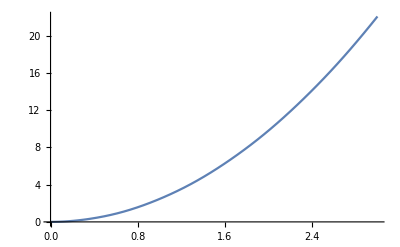

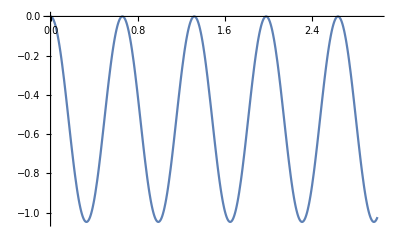

```mathematica
Plot[s[t]/.sol1[[1]],{t,0,3}]
Plot[ϕ[t]/.sol1[[1]],{t,0,3}]
```